Matrices Encoding Images
Images are encoded per pixel, where each element in the matrix represents brightness per pixel.

```mathematica
Image[({{0.1, 0.9, 0.3}, {0.4, 0.5, 0.6}, {0.7, 0.7, 0.9}})]
```

-Graphics-

Images can also be colored where each element in the matrix represents RGB values per pixel

```mathematica
Image[({{({{0}, {0.6}, {0}}), ({{0.4}, {0.1}, {0.8}}), ({{0.7}, {0.9}, {0.7}})}, {({{1}, {0}, {0.9}}), ({{0.6}, {0.6}, {1}}), ({{1}, {0.8}, {0.3}})}}), ColorSpace -> "RGB"]
```

-Graphics-

Matrix Multiplication
Given a 3x2 matrix, A, and a 2x3 matrix B, you can compute the product of the matrix

```mathematica
A={{2, 1}, {4, 6}, {-1, 3}};
B=  {{4, 1, 0}, {1, -1, 2}};
MatC = {{4, 1, 0}, {1, -1, 2}, {1, 2, -1}};
MatI = {{0, 0, 1}, {0, 1, 0}, {1, 0, 0}};
MatI2={{1, 0}, {0, 1}};
```

```mathematica
MatrixForm[MatI.MatC]
MatrixForm[MatC]
```

(1 | 2 | -1
1 | -1 | 2
4 | 1 | 0)

(4 | 1 | 0
1 | -1 | 2
1 | 2 | -1)

```mathematica
MatrixForm[Transpose[A]]
```

(2 | 4 | -1
1 | 6 | 3)

Vectors
The following vectors:
red = [-0.5
-1], blue = [1
2], purple = [2
0.5]
can be presented as arrow in a 2 dimensional vector space

{0,0}

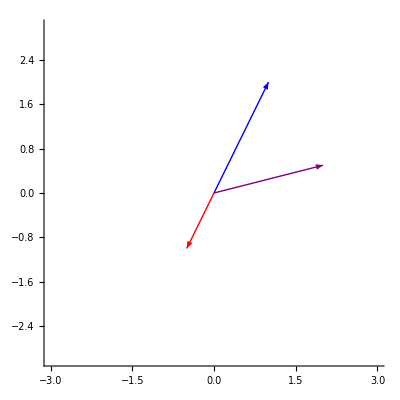

```mathematica
origin = {0,0}
Graphics[{{RGBColor[1,0,0],Thick,Arrow[{origin,{-0.5,-1}}]},{Blue,Thick,Arrow[{origin,{1,2}}]},{RGBColor[0.5,0,0.5],Thick,Arrow[{origin,{2,0.5}}]}},Axes->{True,True},PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
origin3d = {0,0,0};
Graphics3D[{{Red,Thick,Arrow[{origin3d,{1,0,0}}]},{Blue,Thick,Arrow[{origin3d,{0,1,1}}]},{Green,Thick,Arrow[{origin3d,{0,0,1}}]}},Axes->{True,True,True},AxesOrigin->{0,0,0},Boxed->False, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}]
```

-Graphics3D-

```mathematica
VectorAddRender[3{2,0},2{1,1},{{-8,8},{-8,8}}]
```

VectorAddRender[{6,0},{2,2},{{-8,8},{-8,8}}]

```mathematica
m=Table[{i+1,j+1},{i,-6,4},{j,-6,4}];
```

```mathematica
span=Flatten[m,1];
shearedspan = Map[Shear,span];
Shear[v_]:={{0.5,0.5},{0.5,0}}.v
ColorVector[v_]:=RGBColor[(v[[1]]+5)/10,(v[[2]]+5)/10,0]
colorgrid=Map[ColorVector,span];
```

```mathematica
MakeArrow[v_]:=Arrow[{origin,v}]
MakeTArrow[v_]:={Opacity[0.2],MakeArrow[v]}
MakeT2Arrow[v_]:={Opacity[0.5],Red,MakeArrow[v]}
MakeColorArrow[c_,v_]:={c,Thick,MakeArrow[v]}
AutoColorArrow[v_]:={RGBColor[(v[[1]]+5)/10,0,(v[[2]]+5)/10],MakeArrow[v]}
MakePoint[v_]:={PointSize[Large],Point[v]}
MakeGrid[v_]:={{Line[{{v[[1]],-10},{v[[1]],10}}]},{Line[{{-10,v[[2]]},{10,v[[2]]}}]}}
```

```mathematica
vectorspan = Map[MakeArrow,span];
shearedvectorspan = Map[MakeArrow,shearedspan];
pointspan= Map[MakePoint,span];
gridspan = Flatten[Map[MakeGrid,span],1];
shearedcolorvectorspan=Thread[List[colorgrid,shearedvectorspan]];
colorvectorspan=Thread[List[colorgrid,vectorspan]];
```

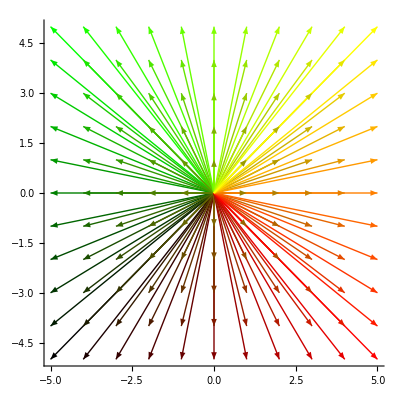

```mathematica
Graphics[colorvectorspan,Axes->{True,True},PlotRange->{{-5,5},{-5,5}}]
```

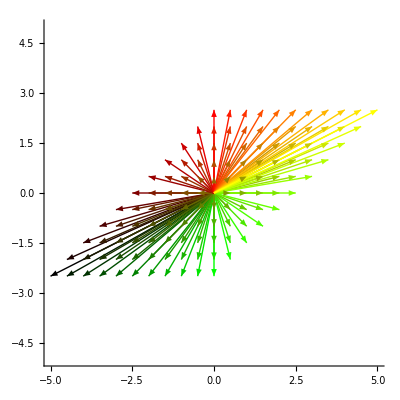

```mathematica
Graphics[shearedcolorvectorspan,Axes->{True,True},PlotRange->{{-5,5},{-5,5}}]
```

```mathematica
Thread[List[{1,2,3},{4,5,6}]]
```

```mathematica
{{1,4},{2,5},{3,6}}
```

{{1,4},{2,5},{3,6}}

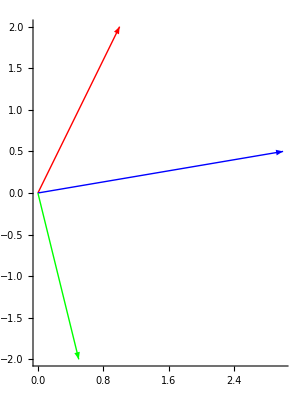

```mathematica
redRGB=RGBColor[{1,0,0}];
blueRGB=RGBColor[{0,0,1}];
greenRGB=RGBColor[{0,1,0}];
v1={1,2};
v2={3,0.5};
v3= {0.5,-2};
Graphics[{MakeColorArrow[redRGB,v1],MakeColorArrow[blueRGB,v2],MakeColorArrow[greenRGB,v3]},Axes->{True,True}]
```

```mathematica
ColorAdd[c1_,c2_]:=RGBColor[{(c1[[1]][[1]]+c2[[1]][[1]])/2,(c1[[1]][[2]]+c2[[1]][[2]])/2,(c1[[1]][[3]]+c2[[1]][[3]])/2}]
```

```mathematica
ColorAdd[redRGB,blueRGB];
```

```mathematica
VectorAddRender[v1_,v2_,plotrange_]:=Graphics[{MakeColorArrow[redRGB,v1],MakeColorArrow[blueRGB,v2],MakeColorArrow[ColorAdd[redRGB,blueRGB],v1+v2],{redRGB,Dashed,Arrow[{v1,v1+v2}]},{blueRGB,Dashed,Arrow[{v2,v1+v2}]}},Axes->{True,True},PlotRange->plotrange]
```

```mathematica
VectorAddRender[v2,v3,{{-5,5},{-5,5}}]
```

-Graphics-

```mathematica
origin3d={0,0,0};
Make3dArrow[v_]:=Arrow[Tube[{origin3d,v}]]
Make3dColorArrow[c_,v_]:={c,Thick,Make3dArrow[v]}
Make3dPoint[v_]:={PointSize[Large],Point[v]}
```

```mathematica
VectorAddRender3d[v1_,v2_]:=Graphics3D[{Make3dColorArrow[redRGB,v1],Make3dColorArrow[blueRGB,v2],Make3dColorArrow[ColorAdd[redRGB,blueRGB],v1+v2],{redRGB,Dashed,Arrow[{v1,v1+v2}]},{blueRGB,Dashed,Arrow[{v2,v1+v2}]}},Axes->{True,True,True},AxesOrigin->origin3d]
```

```mathematica
VectorAddRender3d[{1,3,1},{-2,1,-3}]
```

-Graphics3D-

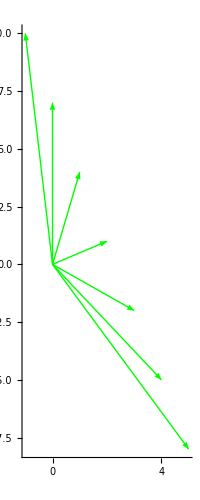

```mathematica
g1={2,1};
g2={-1,3};
generatedArrows=Map[MakeColorArrow[greenRGB,#]&,Table[g1+i g2,{i,-3,3}]];
Graphics[generatedArrows,Axes-> {True,True}]
```

```mathematica
generatedArrows
```

{{RGBColor[{0, 1, 0}],Thickness[Large],Arrow[{{0,0},{5,-8}}]},{RGBColor[{0, 1, 0}],Thickness[Large],Arrow[{{0,0},{4,-5}}]},{RGBColor[{0, 1, 0}],Thickness[Large],Arrow[{{0,0},{3,-2}}]},{RGBColor[{0, 1, 0}],Thickness[Large],Arrow[{{0,0},{2,1}}]},{RGBColor[{0, 1, 0}],Thickness[Large],Arrow[{{0,0},{1,4}}]},{RGBColor[{0, 1, 0}],Thickness[Large],Arrow[{{0,0},{0,7}}]},{RGBColor[{0, 1, 0}],Thickness[Large],Arrow[{{0,0},{-1,10}}]}}

```mathematica
Table[Graphics[MakeColorArrow[greenRGB,g1+i g2],Axes -> {True,True},PlotRange-> {{-10,10},{-10,10}}],{i,-3,3,0.2}];
```

```mathematica
g1={2,1};
g2={-1,3};
Manipulate[Graphics[MakeColorArrow[greenRGB,i g1+j g2],Axes -> {True,True},PlotRange-> {{-10,10},{-10,10}}],{i,-3,3},{j,-3,3}]
```

```mathematica
g4={1,-2,0};
g5 = {-1,0.5,1};
g6={0,2,1};
Manipulate[Graphics3D[Make3dColorArrow[greenRGB,scalar1 g4 + scalar2 g5 + scalar3 g6], Axes -> {True,True,True}, PlotRange->{{-5,5},{-5,5},{-5,5}}],{scalar1,-3,3},{scalar2,-3,3},{scalar3,-3,3}]
```

```mathematica
b1={1,1,4};
b2={-1,3,9};
b3 = {3,2,1};
generated3dArrows=Map[Make3dColorArrow[Blue,#]&,Flatten[Table[b1+i b2+j b3,{i,-4,4},{j,-4,4}],1]];
```

```mathematica
Graphics3D[generated3dArrows,Axes->{True,True,True}]
```

-Graphics3D-

```mathematica
i={1,0};
j={0,1};
MakeSpan[v1_,v2_]:=Flatten[Table[i v1+j v2,{i,-10,10},{j,-10,10}],1]
RenderSpan[v1_,v2_]:=Graphics[Join[Map[MakeArrow,MakeSpan[v1,v2]],{{RGBColor[1,0,0],Thick,Arrow[{origin,v1}]},{Blue,Thick,Arrow[{origin,v2}]}}],Axes->{True,True},PlotRange->{{-5,5},{-5,5}}]
```

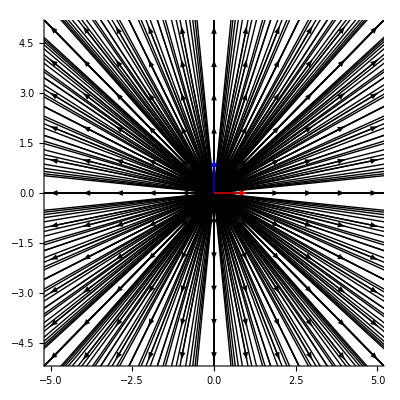

```mathematica
RenderSpan[{1,0},{0,1}]
```

```mathematica
Make3dSpan[v1_,v2_,v3_]:=Flatten[Table[i v1+j v2+k v3,{i,-5,5,2},{j,-5,5,2},{k,-5,5,2}],2]
Render3dSpan[v1_,v2_,v3_]:=Graphics3D[Join[{Opacity[0.4],Map[Make3dArrow,Make3dSpan[v1,v2,v3]]},{{Opacity[1],Red,Thick,Arrow[Tube[{origin3d,v1}]]},{Opacity[1],Blue,Thick,Arrow[Tube[{origin3d,v2}]]},{Opacity[1],Green,Thick,Arrow[Tube[{origin3d,v3}]]}}],Axes->{True,True,True},Boxed->True,AxesOrigin->origin3d,PlotRange->{{-5,5},{-5,5},{-5,5}}]
```

```mathematica
g1=Render3dSpan[{1,0,0},{0,1,0},{0,0,1}];
g2=Render3dSpan[{1,1,0},{0.5,0.5,0},{0,0,1}];
g3=Render3dSpan[{1,1,0},{0.5,0.5,0},{-1,-1,0}];
Show[GraphicsGrid[{{g1,g2,g3}}],ImageSize-> Full]
```

-Graphics-

```mathematica
Graphics3D[Make3dColorArrow[redRGB,{1,3,-2}],Axes-> {True,True,True},PlotRange->{{-5,5},{-5,5},{-5,5}},AxesOrigin-> {0,0,0}]
```

-Graphics3D-

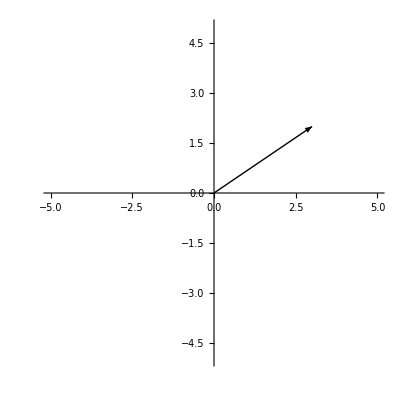

```mathematica
vector={3,2};
Graphics[MakeArrow[vector],Axes->{True,True},AxesOrigin->origin,PlotRange->{{-5,5},{-5,5}}]
```

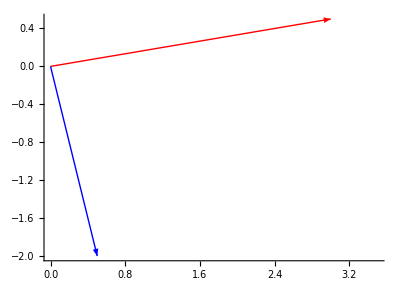

```mathematica
Graphics[{MakeColorArrow[redRGB,v2],MakeColorArrow[blueRGB,v3]},Axes->{True,True},PlotRange->{{0,3.5},{-2,0.5}}]
```

```mathematica
VectorAddRender[v2,v3]
```

VectorAddRender[{3,0.5},{0.5,-2}]

```mathematica
Manipulate[Graphics[MakeColorArrow[redRGB,i v2],Axes->{True,True},PlotRange->{{-7,7},{-7,7}}],{{i,1,"scalar"},-2,4}]
```

```mathematica
matA={{3, 2, 1}, {6, 4, 8}, {1, 0, 1}};
matB={{0, 1, 3}, {2, 1, 4}, {8, 2, 3}};
matC={{2}, {1}, {4}};
matD={{6, 8, 1}};
IdentityMat={{1, 0, 0}, {0, 1, 0}, {0, 0, 1}};
```

```mathematica
MatrixForm[ IdentityMat.matA]
MatrixForm[A]
```

(3 | 2 | 1
6 | 4 | 8
1 | 0 | 1)

(2 | 1
4 | 6
-1 | 3)

```mathematica
LinTransform[tmatrix_,vectors_]:=Graphics[Join[Map[MakeTArrow,vectors],Map[MakeT2Arrow,Map[tmatrix.#&,vectors]]],Axes->{True,True}]
```

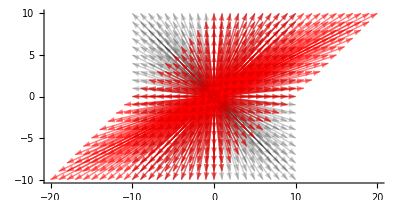

```mathematica
LinTransform[{{1,1},{0,1}},MakeSpan[i,j]]
```

```mathematica
GridTransform[t_,b1_,b2_,vlist_,colors_]:=Graphics[Join[Map[MakeTGrid[t,#]&,MakeSpan[b1,b2]],{MakeColorArrow[Red,t.b1],MakeColorArrow[Blue,t.b2]},MapThread[MakeColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True},PlotRange->{{-5,5},{-5,5}}]
GridTransform3d[t_,b1_,b2_,b3_,vlist_,colors_]:=Graphics3D[Join[Map[MakeTGrid3d[t,#]&,Make3dSpan[b1,b2,b3]],{Make3dColorArrow[Red,t.b1],Make3dColorArrow[Blue,t.b2],Make3dColorArrow[Green,t.b3]},MapThread[Make3dColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True,True},PlotRange->{{-3,3},{-3,3},{-3,3}}]
```

```mathematica
G=MakeGrid[{1,1}]
```

{{Line[{{1,-10},{1,10}}]},{Line[{{-10,1},{10,1}}]}}

```mathematica
{{Line[{{1,-10},{1,10}}]},{Line[{{-10,1},{10,1}}]}}
```

{{Line[{{1,-10},{1,10}}]},{Line[{{-10,1},{10,1}}]}}

```mathematica
MakeTGrid[t_,v_]:={{Opacity[0.01],Thin,Line[{t.{v[[1]],-10},t.{v[[1]],10}}]},{Opacity[0.01],Thin,Line[{t.{-10,v[[2]]},t.{10,v[[2]]}}]}}
MakeTGrid3d[t_,v_]:={{Opacity[0.5],Thin,Line[{t.{v[[1]],v[[2]],-10},t.{v[[1]],v[[2]],10}}]},{Opacity[0.5],Thin,Line[{t.{-10,v[[2]],v[[3]]},t.{10,v[[2]],v[[3]]}}]},{Opacity[0.5],Thin,Line[{t.{v[[1]],-10,v[[3]]},t.{v[[1]],10,v[[3]]}}]}}
```

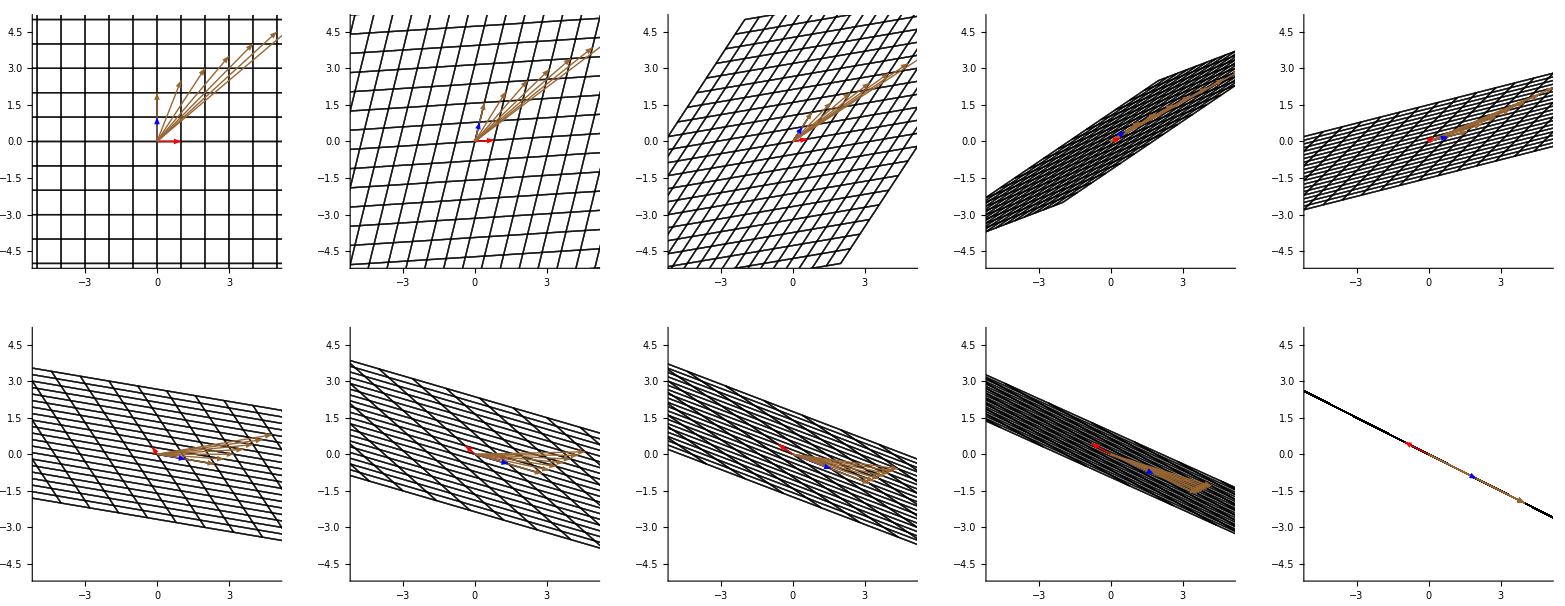

```mathematica
colorlist={Red,Blue,Green,Yellow,Black,Brown,Orange};
identity={{1,0},{0,1}};
rotate90={{0,-1},{1,0}};
hflip={{1,0},{0,-1}};
stretchx={{2,0},{0,1}};
shrinkx={{0.5,0},{0,1}};
stretchy={{1,0},{0,2}};
stretchxy={{2,0},{0,2}};
sheary={{1,0},{1,1}};
shearx={{1,1},{0,1}};
shrink={{0,1},{0,2}};
g1=GridTransform[identity,{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g12=GridTransform[{{0.8,0.2},{0.05,0.8}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g2=GridTransform[{{0.6,0.4},{0.1,0.6}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g23=GridTransform[{{0.4,0.6},{0.15,0.4}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g3=GridTransform[{{0.2,0.8},{0.2,0.2}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g34=GridTransform[{{0.0,1},{0.25,0.0}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g4=GridTransform[{{-0.2,1.2},{0.3,-0.2}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g46=GridTransform[{{-0.4,1.4},{0.35,-0.4}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g5=GridTransform[{{-0.6,1.6},{0.4,-0.6}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g56=GridTransform[{{-0.8,1.8},{0.45,-0.8}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},
{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
g6=GridTransform[{{-1,2},{0.5,-1}},{1,0},{0,1},{{0,2},{1,2.5},{2,3},{3,3.5},{4,4},{5,4.5},{6,5}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown}];
GraphicsGrid[{{g1,g12,g2,g23,g3},{g4,g46,g5,g56,g6}}]
```

```mathematica
rotate90.shearx
```

{{0,-1},{1,1}}

```mathematica
Manipulate[Show[GridTransform[identity-0.02i(identity-rotate90),{0,1},{1,0},{{1,1},{2,1},{-2,-0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>"/rotate90/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform[identity-0.02i(identity-rotate90),{0,1},{1,0},{{1,1},{2,1},{-2,-0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
```

```mathematica
m1=Manipulate[Import[NotebookDirectory[]<>"/rotate90/"<>ToString[i]<>".png"],{i,0,50,1},ContentSize->{400, 400}]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>"/rotate90ToShear/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform[rotate90-0.02i(rotate90-shearx),{0,1},{1,0},{{1,1},{2,1},{-2,-0.5},{1,-2}},{Green, Brown,Yellow,Black}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
```

```mathematica
m2=Manipulate[Import[NotebookDirectory[]<>"/rotate90ToShear/"<>ToString[i]<>".png"],{i,0,50,1},ContentSize->{400, 400}]
GraphicsGrid[{{m1,m2}}]
```

```mathematica
MatrixForm[{{1,1},{0,1}}.{{1},{0}}]
```

(1
0)

```mathematica
i
```

{1,0}

```mathematica
j
```

{0,1}

```mathematica
MatrixForm[{{1,1},{0,1}}]
```

(1 | 1
0 | 1)

```mathematica
colors={Green,Yellow,Black,Brown};
vlist={1,2,3,4};
MapThread[MakeColorArrow[#,t.#2]&,{colors,vlist}];
```

```mathematica
t={{2,2,-3},{-2,1,0},{0,0,0}};
t0={{1,0,0},{0,1,0},{0,0,1}};
b1={1,0,0};
b2={0,1,0};
b3={0,0,1};
g1=GridTransform3d[t0,b1,b2,b3,{{2,0,1}},{Brown}];
g2=GridTransform3d[t,b1,b2,b3,{{2,0,1}},{Brown}];
GraphicsGrid[{{g1,g2}}]
```

-Graphics-

```mathematica
MapThread[Export[NotebookDirectory[]<>"/transform3d1/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform3d[t0-0.02i(t0-t),b1,b2,b3,{{2,0,1}},{Brown}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
Manipulate[Import[NotebookDirectory[]<>"/transform3d1/"<>ToString[i]<>".png"],{i,0,50,1},ContentSize->{400, 400}]
```

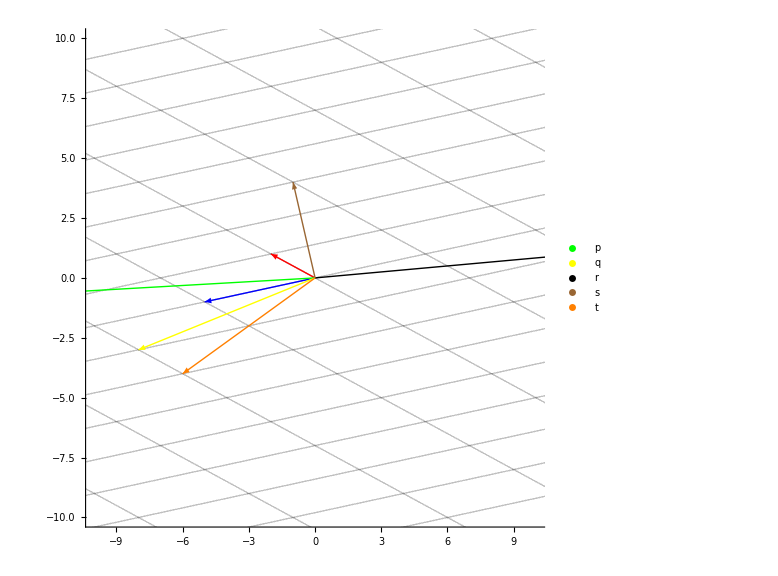

```mathematica
GridTransformLegends[t_,b1_,b2_,vlist_,colors_,legends_]:=Legended[Graphics[Join[Map[MakeTGrid[t,#]&,MakeSpan[b1,b2]],{MakeColorArrow[Red,t.b1],MakeColorArrow[Blue,t.b2]},MapThread[MakeColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True},PlotRange->{{-10,10},{-10,10}}],PointLegend[colors,legends]]
g1=GridTransformLegends[{{1, 0}, {0, 1}},{1,0},{0,1},{{2,3},{-1,2},{-1,-2},{3,-1},{-2,2}},{Green,Yellow,Black,Brown,Orange},{"p","q","r","s","t"}];g2=GridTransformLegends[({{-2, 3}, {1, 2}}).({{1, 0}, {0, -1}}).({{1, 1}, {0, 1}}),{1,0},{0,1},{{2,3},{-1,2},{-1,-2},{3,-1},{-2,2}},{Green,Yellow,Black,Brown,Orange},{"p","q","r","s","t"}];
Show[GraphicsGrid[{{g1,g2}}],ImageSize-> Full];
Show[g2,ImageSize->Large]
```

```mathematica
MatrixForm[({{-2, 3}, {1, 2}}).({{1, 0}, {0, -1}}).({{1, 1}, {0, 1}})]
```

(-2 | -5
1 | -1)

```mathematica
Det[{{-2, -5}, {1, -1}}]
```

7

```mathematica
Det[({{1, -1, -2}, {2, 3, -4}, {-2, 1, 4}})]
Det[({{2, -4, 2}, {0, 8, 1}, {-3, 2, 5}})]
```

0

136

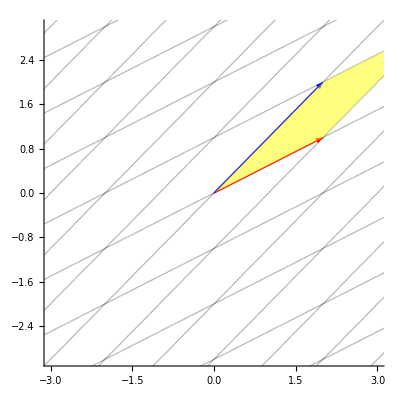

```mathematica
GridTransformDeterminant[t_,b1_,b2_]:=Graphics[Join[Map[MakeTGrid[t,#]&,MakeSpan[b1,b2]],{MakeColorArrow[Red,t.b1],MakeColorArrow[Blue,t.b2]},{Yellow,Opacity[0.5],Polygon[{t.{0,0},t.{0,1},t.{1,1},t.{1,0}}]}],Axes-> {True,True},PlotRange->{{-3,3},{-3,3}}]
GridTransformDeterminant[shearx.sheary.stretchy,{1,0},{0,1}]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>"/transform2dDet/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransformDeterminant[identity-0.02i(identity-shearx.rotate90.stretchy),{1,0},{0,1}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
Manipulate[Import[NotebookDirectory[]<>"/transform2dDet/"<>ToString[i]<>".png"],{i,0,50,1},ContentSize->{400, 400}]
```

```mathematica
GridTransform3dDet[t_,b1_,b2_,b3_,plotrange_:{{-10,10},{-10,10},{-10,10}}]:=Graphics3D[Join[{Make3dColorArrow[Red,t.b1],Make3dColorArrow[Blue,t.b2],Make3dColorArrow[Green,t.b3]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.{1,0,0},t.{1,1,0},t.{0,1,0}}]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,1},t.{1,0,1},t.{1,1,1},t.{0,1,1}}]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.{0,0,1},t.{1,0,1},t.{1,0,0}}]},{Yellow,Opacity[0.5],Polygon[{t.{0,1,0},t.{0,1,1},t.{1,1,1},t.{1,1,0}}]},{Yellow,Opacity[0.5],Polygon[{t.{0,0,0},t.{0,0,1},t.{0,1,1},t.{0,1,0}}]},{Yellow,Opacity[0.5],Polygon[{t.{1,0,0},t.{1,0,1},t.{1,1,1},t.{1,1,0}}]}],Axes-> {True,True,True},PlotRange->plotrange]
t1={{0.9,1,0},{0,1,-0.3},{1,0,1}};
t2=Inverse[t1];
g1=GridTransform3d[t0,{1,0,0},{0,1,0},{0,0,1}];
g2=GridTransform3d[t1,{1,0,0},{0,1,0},{0,0,1}];
g3=GridTransform3d[t2.t1,{1,0,0},{0,1,0},{0,0,1}];
GraphicsGrid[{{g1,g2,g3}}];
g1=GridTransform3dDet[({{1, -1, -2}, {2, 3, -4}, {-2, 1, 4}}),{1,0,0},{0,1,0},{0,0,1}]
Render3dSpan[{1,2,-2},{-1,3,1},{-2,-4,4}];
```

-Graphics3D-

```mathematica
MatrixForm[Inverse[{{3, 0, 2}, {1, -2, 2}, {-1, 3, 2}}]]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>"/transform3dDet/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransform3dDet[t0-0.02i(t0-({{1, -1, -2}, {2, 3, -4}, {-2, 1, 4}})),{1,0,0},{0,1,0},{0,0,1},{{-5,5},{-5,5},{-5,5}}],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
Manipulate[Import[NotebookDirectory[]<>"/transform3dDet/"<>ToString[i]<>".png"],{i,0,50,1},ContentSize->{400, 400}]
```

```mathematica
{{-1,2},{0.5,-1}}.{6,5}
```

{4.,-2.}

```mathematica
GridTransformExtra[t_,b1_,b2_,vlist_,colors_,v_]:=Graphics[Join[Map[MakeTGrid[t,#]&,MakeSpan[b1,b2]],{MakeColorArrow[Red,t.b1],MakeColorArrow[Blue,t.b2],MakeColorArrow[Brown,v]},MapThread[MakeColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True},PlotRange->{{-6,6},{-6,6}}]
```

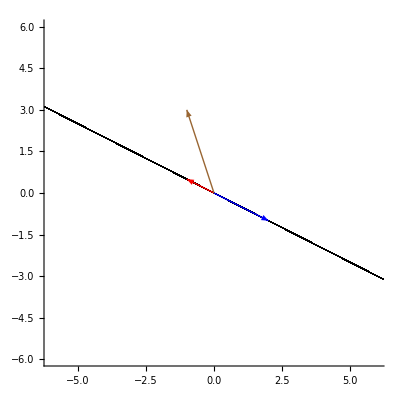

```mathematica
g1=GridTransform[identity,{1,0},{0,1},{},{}];
g3=GridTransformExtra[{{-1,2},{0.5,-1}},{1,0},{0,1},{},{},{-1,3}]
```

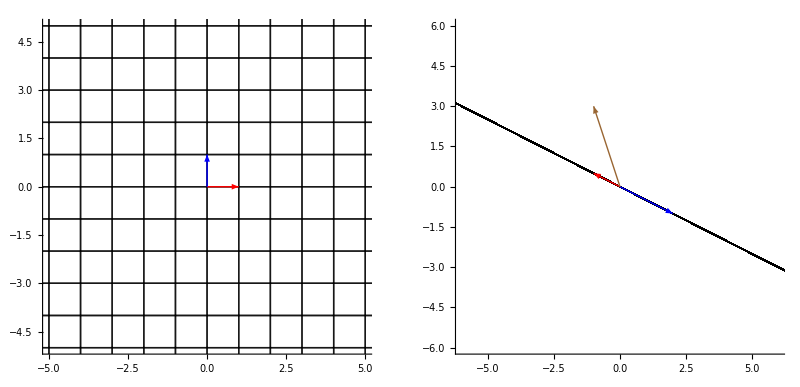

```mathematica
GraphicsGrid[{{g1,g3}}]
```

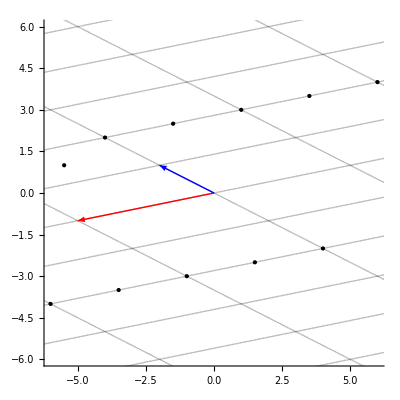

```mathematica
GridTransformPoint[t_,b1_,b2_,vlist_]:=Graphics[Join[{PointSize[Large],Point[Map[t.#&,vlist]]}, Map[MakeTGrid[t,#]&,MakeSpan[b1,b2]],{MakeColorArrow[Red,t.b1],MakeColorArrow[Blue,t.b2]}],Axes-> {True,True},PlotRange->{{-6,6},{-6,6}}]
vlist = {{-2,2},{-2,1.5},{-2,1},{-2,.5},{-2,0},
{-2,-2},{-2,-1.5},{-2,-1},{-2,-.5},{2,0},
{2,-2},{2,-1.5},{2,-1},{2,-.5},
{-1.5,-2},{-1,-2},{-0.5,-2},{0,-2},
{1.5,-2},{1,-2},{0.5,-2},
{-1.5,2},{-1,2},{-0.5,2},{0,2},
{0.5,1.5},{1.5,0.5},{1,1}};
GridTransformPoint[({{-2, 3}, {1, 2}}).({{1, 0}, {0, -1}}).({{1, 1}, {0, 1}}),{0,1},{1,0},vlist]
```

```mathematica
MapThread[Export[NotebookDirectory[]<>"/transformPoint/"<>ToString[#2]<>".png",#,ImageResolution-> 100]&,{Table[Show[GridTransformPoint[identity-0.02i(identity-({{-2, 3}, {1, 2}}).({{1, 0}, {0, -1}}).({{1, 1}, {0, 1}})),{1,0},{0,1},vlist],ImageSize-> Large],{i,0,50}],Table[i,{i,0,50}]}];
Manipulate[Import[NotebookDirectory[]<>"/transformPoint/"<>ToString[i]<>".png"],{i,0,50,1},ContentSize->{400, 400}]
```

```mathematica
MatrixForm[{{1,0},{1,}}]
```

(1 | 0
1 | Null)

```mathematica
Det[({{-2, 3}, {1, 2}}).({{1, 0}, {0, -1}}).({{1, 1}, {0, 1}})]
```

7

```mathematica
MatrixForm[({{-2, 3}, {1, 2}}).({{1, 0}, {0, -1}}).({{1, 1}, {0, 1}})]
```

(-2 | -5
1 | -1)

```mathematica
Det[{{-2, 3}, {1, 2}}]
```

-7

```mathematica
MatrixForm[({{1, 0}, {0, -1}}).({{1, 1}, {0, 1}})]
```

(1 | 1
0 | -1)

```mathematica
MatrixForm[({{5/14, -3/14, -1/7}, {1/7, -2/7, 1/7}, {-1/28, 9/28, 3/14}}).({{3, 0, 2}, {1, -2, 2}, {-1, 3, 2}})]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Inverse[{{3, 0, 2}, {1, -2, 2}, {-1, 3, 2}}]
```

{{5/14,-3/14,-1/7},{1/7,-2/7,1/7},{-1/28,9/28,3/14}}

```mathematica
MatrixForm[({{0.5, 0}, {0, 1}}).({{2, 0}, {0, 1}})]
```

(1. | 0.
0. | 1.)

```mathematica
MatrixForm[Inverse[{{3, 2}, {-1, 2}}]]
```

(1/4 | -1/4
1/8 | 3/8)

```mathematica
Det[{{2, 1, 0}, {3, 1, -1}, {-2, -1, -2}}]
```

2

```mathematica
Det[({{-3/2, 1, -1/2}, {4, -2, 1}, {-1/2, 0, -1/2}})]
```

1/2

```mathematica
MatrixForm[Inverse[{{4, 0.5}, {-2, -1}}]]
```

(0.333333 | 0.166667
-0.666667 | -1.33333)

```mathematica
MatrixForm[({{-2, 3}, {3, -1}}).({{0.143, 0.428}, {0.429, 0.285}})]
```

(1.001 | -0.001
-5.55112×10^-17 | 0.999)

```mathematica
MatrixForm[({{0.1428, 0.4286}, {0.4285, 0.2857}}).({{-2, 3}, {3, -1}})]
```

(1.0002 | -0.0002
0.0001 | 0.9998)

```mathematica
MatrixForm[{{2, 2, -3}, {-2, 1, 0}}.{{2}, {0}, {1}}]
```

(1
-4)

```mathematica
MatrixForm[{{2, 2, -3}, {-2, 1, 0}, {0, 0, 0}}.{{2}, {0}, {1}}]
```

(1
-4
0)

```mathematica
Inverse[{{2, 2, -3}, {-2, 1, 0}}]
```

Inverse::matsq: Argument {{2,2,-3},{-2,1,0}} at position 1 is not a non-empty square matrix.

Inverse[{{2,2,-3},{-2,1,0}}]

```mathematica
Inverse[{{2, 2, -3}, {-2, 1, 0}, {0, 0, 0}}]
```

Inverse::sing: Matrix {{2,2,-3},{-2,1,0},{0,0,0}} is singular.

Inverse[{{2,2,-3},{-2,1,0},{0,0,0}}]

```mathematica
MatrixForm[{{3, 0}, {-1, -2}, {2, 1}}.{{1}, {2}}]
```

(3
-5
4)

```mathematica
GridTransformThreexTwo[t_,vlist_,colors_]:=Graphics3D[Join[Map[MakeTGrid3d[Transpose[ArrayReshape[Transpose[t],{3,3},0]],#]&,Make3dSpan[IdentityMatrix[3][[All,1]],IdentityMatrix[3][[All,2]],IdentityMatrix[3][[All,3]]]],{Make3dColorArrow[Red,t.IdentityMatrix[2][[All,1]]],Make3dColorArrow[Blue,t.IdentityMatrix[2][[All,2]]]},MapThread[Make3dColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True,True},PlotRange->{{-7,7},{-7,7},{-7,7}}]
```

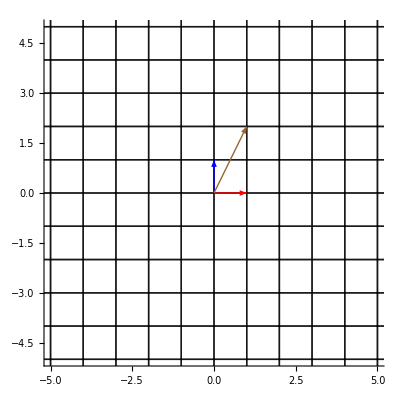

```mathematica
g1 = GridTransform[IdentityMatrix[2],{1,0},{0,1},{{1,2}},{Brown}];
g2 = GridTransformThreexTwo[({{3, 0}, {-1, -2}, {2, 1}}),{{1,2}},{Brown}];
Show[GraphicsGrid[{{g1,g2}}],ImageSize->Full]
```

```mathematica
Export["/Users/rub/Google Drive/CMSC 56/nonsquareexpand.png",%603,"PNG"]
```

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/nonsquareexpand.png.

$Failed

```mathematica
GridTransformTwoxThree[t_,vlist_,colors_]:=Graphics[Join[Map[MakeTGridS[t,#]&,MakeSpan[IdentityMatrix[2][[All,1]],IdentityMatrix[2][[All,2]]]],{MakeColorArrow[Red,t.IdentityMatrix[3][[All,1]]],MakeColorArrow[Blue,t.IdentityMatrix[3][[All,2]]],MakeColorArrow[Green,t.IdentityMatrix[3][[All,3]]]},MapThread[MakeColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True},PlotRange->{{-3,3},{-3,3}}]
```

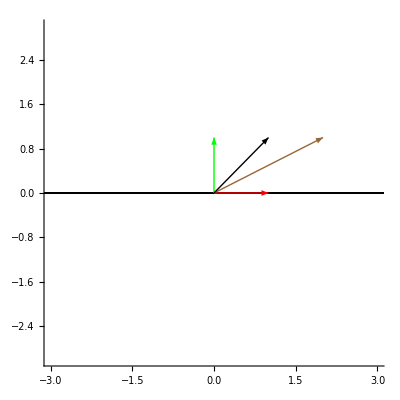

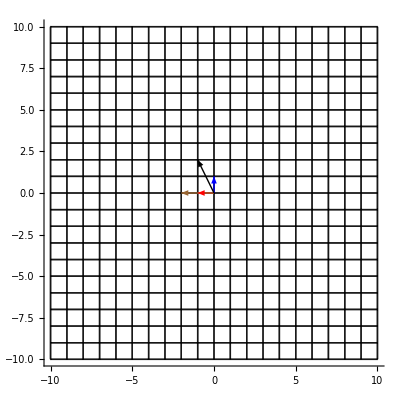

```mathematica
g1=GridTransform3d[IdentityMatrix[3],{1,0,0},{0,1,0},{0,0,1},{{2,0,1},{1,2,1}},{Brown,Black}];
g2=GridTransformTwoxThree[({{1, 0, 0}, {0, 0, 1}}),{{2,0,1},{1,2,1}},{Brown,Black}];
Show[GraphicsGrid[{{g1,g2}}],ImageSize->Full]
```

```mathematica
Export["/Users/rub/Google Drive/CMSC 56/nonsquarereduced.png",%595,"PNG"]
```

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/nonsquarereduced.png.

$Failed

```mathematica
IdentityMatrix[2][[All,1]]
```

{1,0}

```mathematica
F[x_]:=x*x/;x>0
```

```mathematica
F[-2]
```

F[-2]

```mathematica
MatrixForm[ArrayReshape[{1,2,3,4,5,6,7},{5,3},2]]
```

(1 | 2 | 3
4 | 5 | 6
7 | 2 | 2
2 | 2 | 2
2 | 2 | 2)

```mathematica
ArrayReshape[{{2, 2, -3}, {-2, 1, 0}}[[All,1]],{3},0]
```

{2,-2,0}

```mathematica
Dimensions[{1,2,3},]
```

Dimensions::innf: Non-negative integer or Infinity expected at position 2 in Dimensions[{1,2,3},Null].

Dimensions[{1,2,3},Null]

```mathematica
Graphics3D[Map[MakeTGrid[{{2, 2}, {-2, 1}},#]&,MakeSpan[IdentityMatrix[3][[All,1]],IdentityMatrix[3][[All,2]],IdentityMatrix[3][[All,3]]]]]
```

-Graphics3D-

```mathematica
GridTransform[t_,b1_,b2_,vlist_,colors_]:=Graphics[Join[Map[MakeTGrid[t,#]&,MakeSpan[b1,b2]],{MakeColorArrow[Red,t.b1],MakeColorArrow[Blue,t.b2]},MapThread[MakeColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
v={1,0,0};
t=({{2, 2, -3}, {-2, 1, 0}});
MakeTGridS[t_,v_]:={{Opacity[0.1],Thin,Line[{t.{v[[1]],-10,0},t.{v[[1]],10,0}}]},{Opacity[0.1],Thin,Line[{t.{-10,v[[2]],0},t.{10,v[[2]],0}}]}}
```

```mathematica
{{2,2,-3},{-2,1,0}}.{{1},{-10}}
```

Dot::dotsh: Tensors {{2,2,-3},{-2,1,0}} and {{1},{-10}} have incompatible shapes.

{{2,2,-3},{-2,1,0}}.{{1},{-10}}

```mathematica
MatrixForm[ArrayReshape[({{2, 2, -3}, {-2, 1, 0}}),{2,2}]]
```

(2 | 2
-3 | -2)

```mathematica
Map[MakeTGrid[ArrayReshape[t,{2,2}],#]&,MakeSpan[Identity[2][[All,1]],Identity[2][[All,2]]]]
```

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 1 of Integer[] does not exist.

Part::partw: Part 2 of Integer[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{Opacity[0.1],Thickness[Tiny],Line[{{-60,80},{-20,40}}]},{Opacity[0.1],Thickness[Tiny],Line[{{-20+2 Integer[],30-2 Integer[]},{20+2 Integer[],-30-2 Integer[]}}]}},439,{{Opacity[0.1],Thickness[Tiny],Line[{{20,-40},{60,-80}}]},{Opacity[0.1],1,Line[{{1,1},1}]}}}
 |  |  |  |

```mathematica
Dimensions[{{2,2,-3},{-2,1,0}}]
```

{2,3}

```mathematica
Dimensions[{{1},{-10}}]
```

{2,1}

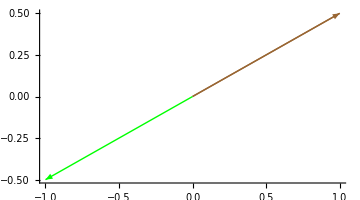

```mathematica
a = {1,0.5};
b = {-1,-0.5};
c={-1,-0.5};
DotProduct[a_,b_]:=Graphics[Join[{MakeColorArrow[Brown,a],MakeColorArrow[Green,b]},{Thick,Brown,Line[{{0,0},b*((a.b)/(b.b))}]},{Dotted,Black,Thick,Line[{b*((a.b)/(b.b)),a}]}],Axes -> {True,True}];
Show[DotProduct[a,b],ImageSize->Medium]
```

```mathematica
a.b
a.c
```

-1.25

-1.25

```mathematica
(0.5a).(0.5a)
```

0.3125

```mathematica
b*((a.b)/(b.b))
```

{1.,0.5}

```mathematica
{0,0}
```

{0,0}

{0.866,0.5}

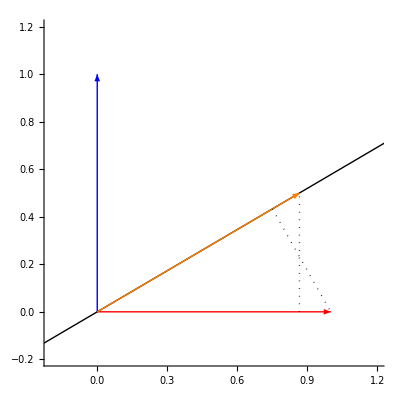

```mathematica
u={0.866,0.5}
i={1,0};
j={0,1};
Graphics[Join[{MakeColorArrow[Red,i]},{MakeColorArrow[Blue,j]},{Line[{10u,-10u}]},{MakeColorArrow[Orange,u]},{Dotted,Black,Thick,Line[{u*((i.u)/(u.u)),i}]},{Dotted,Black,Thick,Line[{i*((u.i)/(i.i)),u}]}],Axes -> {True,True},PlotRange->{{-0.2,1.2},{-0.2,1.2}}]
```

```mathematica
Export["/Users/rub/Google Drive/CMSC 56/test.png",Show[#,ImageSize-> Full],"PNG"]
```

Show::gtype: Slot is not a type of graphics.

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/test.png.

$Failed

```mathematica
GridTransformSequence[t_,vlist_,colorlist_,numplots_]:=
Map[GridTransform[#,IdentityMatrix[2][[All,1]],IdentityMatrix[2][[All,2]],vlist,colorlist]&,Table[IdentityMatrix[2]+i((t-IdentityMatrix[2])*1/numplots),{i,0,numplots}]];
```

```mathematica
MapThread[Export["/Users/rub/Google Drive/CMSC 56/sequence transform2/t"<>ToString[#2]<>".png",Show[#,ImageSize-> Full],"PNG"]&,{GridTransformSequence[({{3, 1}, {0, 2}}),{{1.5,0},{2,0},{2.5,0},{-1,1},{-0.5,0.5},{1,2},{-2,1}},{RGBColor[0.5,0.5,0],RGBColor[0.5,0.6,0],RGBColor[0.5,0.7,0],RGBColor[0,0,0.5],RGBColor[0,0,0.6],Brown,Brown},50],Table[i,{i,0,50}]}];
```

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/sequence transform2/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/sequence transform2/t0.png.

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/sequence transform2/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/sequence transform2/t1.png.

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/sequence transform2/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/sequence transform2/t2.png.

General::stop: Further output of Export::noopen will be suppressed during this calculation.

```mathematica
Dimensions[Table[IdentityMatrix[2]+i({{-3/10, 3/10}, {1/10, 1/10}}),{i,0,10}]]
```

{11,2,2}

```mathematica
(({{-2, 3}, {1, 2}})-IdentityMatrix[2])*1/10
```

{{-3/10,3/10},{1/10,1/10}}

```mathematica
MatrixForm[{{-3/10,3/10},{1/10,1/10}}]
```

(-3/10 | 3/10
1/10 | 1/10)

```mathematica
MapThread[#+#2&,{1,2,3},{4,5,6}]
```

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[#1+#2&,{1,2,3},{4,5,6}].

MapThread[#1+#2&,{1,2,3},{4,5,6}]

```mathematica
MapThread[#1+#2&,{{1,2,3},{4,5,6}}]
```

{5,7,9}

```mathematica
"a"<>ToString[1]
```

a1

```mathematica
RGBColor[1,0.5,1]
```

RGBColor[1, 0.5, 1]

```mathematica
MapThread[Export["/Users/rub/Google Drive/CMSC 56/eigen"<>ToString[#2]<>".png",Show[#,ImageSize-> Full],"PNG"]&,{GridTransformSequence[({{3, 1}, {0, 2}}),{{1.5,0},{2,0},{2.5,0},{-1,1},{-0.5,0.5},{1,2},{-2,1}},{RGBColor[0.5,0.5,0],RGBColor[0.5,0.6,0],RGBColor[0.5,0.7,0],RGBColor[0,0,0.5],RGBColor[0,0,0.6],Brown,Brown},1],Table[i,{i,0,1}]}];
```

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/eigen0.png.

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/eigen1.png.

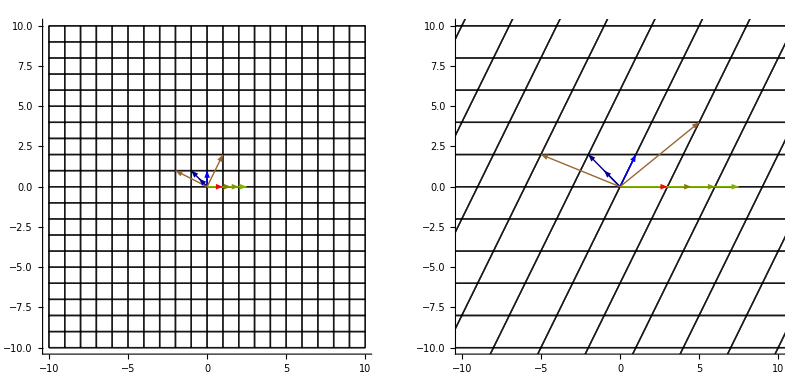

```mathematica
Show[GraphicsGrid[{GridTransformSequence[({{3, 1}, {0, 2}}),{{1.5,0},{2,0},{2.5,0},{-1,1},{-0.5,0.5},{1,2},{-2,1}},{RGBColor[0.5,0.5,0],RGBColor[0.5,0.6,0],RGBColor[0.5,0.7,0],RGBColor[0,0,0.5],RGBColor[0,0,0.6],Brown,Brown},1]}],ImageSize->Full]
```

```mathematica
MapThread[Export["/Users/rub/Google Drive/CMSC 56/sequence transform3/t"<>ToString[#2]<>".png",Show[#,ImageSize-> Full],"PNG"]&,{GridTransformSequence[({{3, 1}, {0, 2}}),{{1.5,0},{1,1},{2,1},{-1,2},{-1,-1},{-1,1},{-2,1}},{Green,Brown,Brown,Brown,Brown,Green,Brown},50],Table[i,{i,0,50}]}];
```

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/sequence transform3/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/sequence transform3/t0.png.

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/sequence transform3/ does not exist.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/sequence transform3/t1.png.

Export::nodir: Directory /Users/rub/Google Drive/CMSC 56/sequence transform3/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

Export::noopen: Cannot open /Users/rub/Google Drive/CMSC 56/sequence transform3/t2.png.

General::stop: Further output of Export::noopen will be suppressed during this calculation.

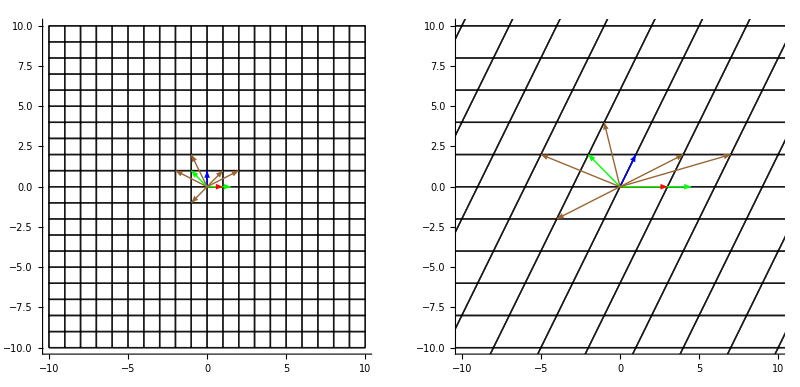

Curry::argt: Curry called with 0 arguments; 1 or 2 arguments are expected.

{Curry[],Curry[],Curry[]}

```mathematica
Show[GraphicsGrid[{GridTransformSequence[({{3, 1}, {0, 2}}),{{1.5,0},{1,1},{2,1},{-1,2},{-1,-1},{-1,1},{-2,1}},{Green,Brown,Brown,Brown,Brown,Green,Brown},1]}],ImageSize->Full]
```

```mathematica
Table[2i,{i,{1,3,7}}]
```

{2,6,14}

```mathematica
F[v_,t_]:=v+t
```

```mathematica
(F[1]&)[3]
```

1

```mathematica
1
```

1

```mathematica
F[3]
```

9

```mathematica
{1,2,3,4}[[5]]
```

Part::partw: Part 5 of {1,2,3,4} does not exist.

{1,2,3,4}⟦5⟧

```mathematica
GridTransform3dRaw[t_,b1_,b2_,b3_,vlist_,colors_]:=Graphics3D[Join[Map[MakeTGrid3d[t,#]&,Make3dSpan[b1,b2,b3]],{Make3dColorArrow[Red,t.b1],Make3dColorArrow[Blue,t.b2],Make3dColorArrow[Green,t.b3]},MapThread[Make3dColorArrow[#,t.#2]&,{colors,vlist}]],Axes-> {True,True,True},PlotRange->{{-3,3},{-3,3},{-3,3}}]
```

```mathematica
GridTransformSequence3d[t_,vlist_,colorlist_,numplots_]:=
Map[GridTransform3dRaw[#,IdentityMatrix[3][[All,1]],IdentityMatrix[3][[All,2]],IdentityMatrix[3][[All,3]],vlist,colorlist]&,Table[IdentityMatrix[3]+i((t-IdentityMatrix[3])*1/numplots),{i,0,numplots}]];
```

```mathematica
MapThread[Export["/Users/rub/Google Drive/Lecture-Notes-And-Resources/CMSC 56/sequence transform4/t"<>ToString[#2]<>".png",Show[#,ImageSize-> Full],"PNG"]&,{GridTransformSequence3d[({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}),{{1.5,0,2},{2,0,1},{2.5,0,3},{-1,1,2},{-0.5,0.5,1},{1,2,1},{-2,1,1}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown},50],Table[i,{i,0,50}]}];
```

```mathematica
MapThread[Export["/Users/rub/Google Drive/Lecture-Notes-And-Resources/CMSC 56/sequence transform5/t"<>ToString[#2]<>".png",Show[#,ImageSize-> Full],"PNG"]&,{GridTransformSequence3d[({{2, 0, 0}, {0, 2, 0}, {0, 0, 2}}),{{1,1,1},{-1,-1-√2,1},{-1,-1+√2,1},{-1,1,2},{-0.5,0.5,1},{1,2,1},{-2,1,1}},{Brown,Brown,Brown,Brown,Brown,Brown,Brown},50],Table[i,{i,0,50}]}];
```

```mathematica
Eigenvectors[({{2, -1, 1}, {1, -1, 2}, {0, 1, 1}})]
Eigenvalues[({{2, -1, 1}, {1, -1, 2}, {0, 1, 1}})]
```

{{1,1,1},{-1,-1-√2,1},{-1,-1+√2,1}}

{2,-√2,√2}

```mathematica
({{-1}, {-1}, {1}})
```

{{-1},{-1},{1}}

```mathematica
Det[({{2, -1, 1}, {1, -1, 2}, {0, 1, 1}})]
```

-4

```mathematica
MapThread[Export["/Users/rub/Google Drive/Lecture-Notes-And-Resources/CMSC 56/sequence transform6/t"<>ToString[#2]<>".png",Show[#,ImageSize-> Full],"PNG"]&,{GridTransformSequence3d[({{2, 2, -3}, {-2, 1, 0}, {0, 0, 0}}),{{2,0,1}},{Brown},50],Table[i,{i,0,50}]}];
```

```mathematica
Eigenvectors[{{2, 0}, {0, 2}}]
Eigenvalues[{{1, 0}, {0, 1}}]
```

{{0,1},{1,0}}

{1,1}

```mathematica
a=({{1}, {-2}});
b=({{2}, {3}});
c=({{3}, {-3}});
d=({{3}, {-1}});
MatrixForm[2b-c]
```

(1
9)

```mathematica
Boop=({{2, 1}, {-1, -1}});
Zoop=({{1, -1}, {0, -0.5}});
Yoop=({{-2, 3}, {-1, 1}});
MatrixForm[Boop.Yoop.Yoop.({{3}, {2}})]
```

(-7
4)

```mathematica
MatrixForm[Boop.Zoop.({{1}, {-1}})]
```

(4.5
-2.5)

```mathematica
MatrixForm[Inverse[Zoop.Yoop]]
```

(1. | 4.
1. | 2.)

```mathematica
Det[Yoop.Zoop.Boop]
```

0.5

```mathematica
MatrixForm[Inverse[Zoop.Yoop]]
```

(1. | 4.
1. | 2.)

```mathematica
Det[Yoop]
```

1

```mathematica
MatrixForm[Inverse[Zoop.Yoop]]
```

(1. | 4.
1. | 2.)

```mathematica
MatrixForm[Inverse[({{3, 2}, {-1, 2}})]]
MatrixForm[Inverse[({{4, 1/2}, {-2, -1}})]]
MatrixForm[Inverse[({{-1.5, 1, -0.5}, {4, -2, 1}, {-0.5, 0, -0.5}})]]
```

(1/4 | -1/4
1/8 | 3/8)

(1/3 | 1/6
-2/3 | -4/3)

(2. | 1. | 0.
3. | 1. | -1.
-2. | -1. | -2.)

```mathematica
F[x_]:=x+1;
G[x_]:=x^2+x;
Plot[F,G,{x,1,100}]
```

SetDelayed::write: Tag List in {{Line[{{1,-10},{1,10}}]},{Line[{{-10,1},{10,1}}]}}[x_] is Protected.

Plot::nonopt: Options expected (instead of {x,1,100}) beyond position 2 in Plot[F,G,{x,1,100}]. An option must be a rule or a list of rules.

Plot[F,G,{x,1,100}]

```mathematica
a({{1}, {0}})+b({{0}, {1}})=({{a}, {b}})
```